```mathematica
xdot=(x^2+y^2)^(Abs[n]/2)*Cos[n*ArcTan[y/x]];
ydot =(x^2+y^2)^(Abs[n]/2)*Sin[n*ArcTan[y/x]];
flow={xdot,ydot}
(* calculate fixed points *)
fixsol=NSolve[flow==0,{x,y},Reals]
```

{(x^2+y^2)^(3/2) Cos[3 ArcTan[y/x]],(x^2+y^2)^(3/2) Sin[3 ArcTan[y/x]]}

{}

```mathematica
{x,y}/.fixsol
```

```mathematica
{{0,0},{0,0},{0,0}
```

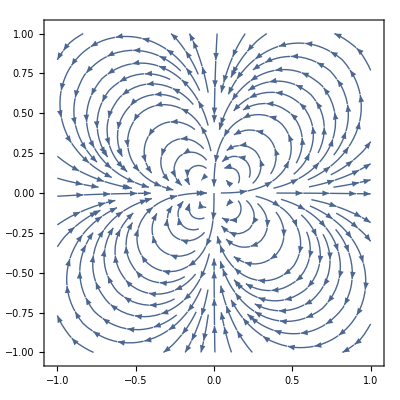

```mathematica
n = 3;
streamplot=Show[
StreamPlot[flow,{x,-1,1},{y,-1,1}]]
```

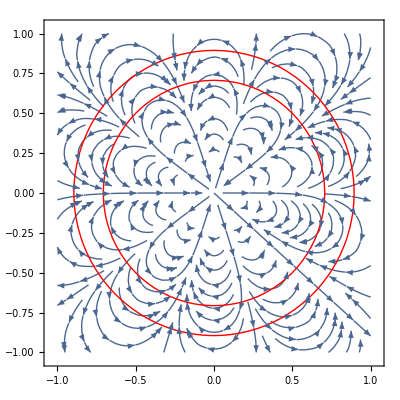

```mathematica
Show[
streamplot,
ContourPlot[x^2+y^2 ==0.8,{x,-1,1},{y,-1, 1},ContourStyle->{Thick,Red}],
ContourPlot[x^2+y^2 ==0.5,{x,-1,1},{y,-1,1},ContourStyle->{Thick,Red}]
]
```